```mathematica
CreateDatabaseFromYahooFile[path_]:=Block[{dataset,dates,prices},
dataset = Import[path];
dates = Map[DateObject,Drop[dataset[[All,1]],1]];
prices = Drop[dataset[[All,5]],1];
Transpose[{dates,prices}]
];
```

```mathematica
dates = Map[FileBaseName,FileNames["*",FileNameJoin[{NotebookDirectory[],"BMV"}]]];
```

```mathematica
files = FileNames["*",FileNameJoin[{NotebookDirectory[],"BMV",First[dates]}]];
```

```mathematica
stocks = Map[FileBaseName,files];
```

```mathematica
stocks
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOF,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
```

```mathematica
dataset = ProgressParallelMap[CreateDatabaseFromYahooFile,files];
```

```mathematica
availableDates = Sort@DeleteDuplicates[Flatten[dataset[[All,All,1]]]];
```

```mathematica
availableDates
```

{Fri 17 Jan 2020 09:30:00GMT-6.,Fri 17 Jan 2020 09:31:00GMT-6.,Fri 17 Jan 2020 09:32:00GMT-6.,Fri 17 Jan 2020 09:33:00GMT-6.,Fri 17 Jan 2020 09:34:00GMT-6.,Fri 17 Jan 2020 09:35:00GMT-6.,768,Mon 20 Jan 2020 14:54:00GMT-6.,Mon 20 Jan 2020 14:55:00GMT-6.,Mon 20 Jan 2020 14:56:00GMT-6.,Mon 20 Jan 2020 14:57:00GMT-6.,Mon 20 Jan 2020 14:58:00GMT-6.,Mon 20 Jan 2020 14:59:00GMT-6.}
 |  |  |  |

```mathematica
GetPriceAtDate[dataset_,date_]:=Block[{pos},
pos = FirstPosition[dataset,{date,_}];
If[pos =!=Missing["NotFound"],Last[Extract[dataset,pos]],None]
];
GetPricesFromDatasetAtDate[dataset_,date_]:=Table[GetPriceAtDate[currentDataset,date],{currentDataset,dataset}];
```

```mathematica
GetPricesFromDatasetAtDate[dataset,DateObject[{2020,1,20,14,54,0},"Instant","Gregorian",-6.]]
```

{105.74,21.62,49.38,15.52,389.89,32.01,36.04,,28.06,7.73,34.15,238.5,74.98,,21.04,113.79,57.82,204.98,87.51,41.05,None,20.37,102.,76.59,149.55,48.65,204.74,205.05,111.66,46.83}

```mathematica
datedDatabase =ProgressMap[{#,GetPricesFromDatasetAtDate[dataset,#]}&,availableDates];
```

```mathematica
FormatPrices[prices_]:=Block[{propagateBackwards,propagateForward},
propagateBackwards = FixedPoint[
SequenceReplace[#,
{
{"null",x_ /;NumberQ[x]}:>Sequence[x,x],
{None,x_ /;NumberQ[x]}:>Sequence[x,x]
}
]&,
prices
];
propagateForward = FixedPoint[
SequenceReplace[#,
{
{x_ /;NumberQ[x],"null"}:>Sequence[x,x],
{x_ /;NumberQ[x],None}:>Sequence[x,x],
{x_ /;NumberQ[x],""}:>Sequence[x,x]
}
]&,
propagateBackwards
];
Return[propagateForward];
];
```

```mathematica
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"EconomicComputations.wl"}]];
```

```mathematica
stocks = Transpose@datedDatabase[[All,2]];
```

```mathematica
stringDates = ProgressMap[DateString[#,"ISODateTime"]&,datedDatabase[[All,1]]];
```

```mathematica
processed = ProgressMap[FormatPrices,stocks];
```

```mathematica
processedPrices = Transpose[processed];
```

```mathematica
toExport = Thread[{stringDates,processedPrices}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BMV",First[dates]<>".wdx"}],toExport]
```

/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/BMV/20-01-2020.wdx

```mathematica
onlyDates = toExport[[All,1]];
onlyPrices = toExport[[All,2]];
```

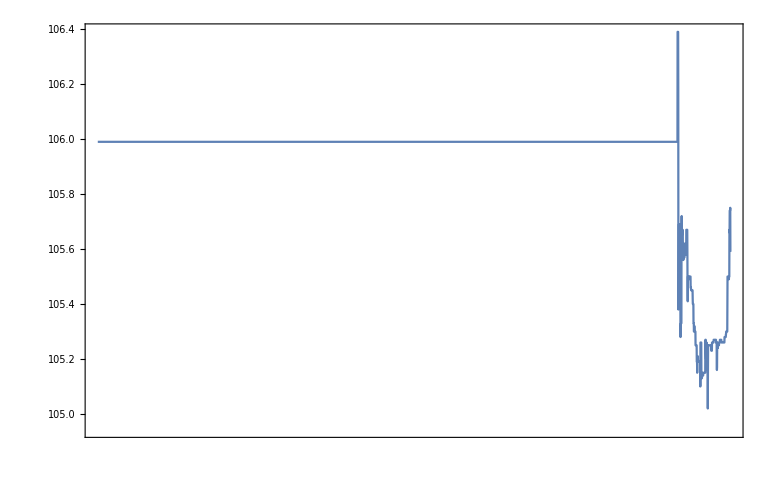

```mathematica
DateListPlot@Transpose[{onlyDates,onlyPrices[[All,1]]}]
```

```mathematica
onlyDates[[1]]
```

2020-01-17T09:30:00

```mathematica
onlyDates[[-1]]
```

2020-01-20T14:59:00

```mathematica
datedDatabase[[All,1]][[1]]
```

Fri 17 Jan 2020 09:30:00GMT-6.